Numeric Solution of the model equations

```mathematica
Clear["Global`*"];
```

### Model parameters (estimated with MATLAB)

```mathematica
θ=0.038999801486034;
b=0.004483480554580;
K=0.998019215315511;
R=3.068968068446540;
L=1.159171764046709 10^-4;
V=12;
TL= 0;
```

### Model equations (x→ω[rad/s], y→i[A])

```mathematica
MomentEquation = θ x'[t] +b x[t] == K y[t]-TL;
KirchoffEquation = L y'[t]+R y[t] ==V-K x[t];
```

### State-space model

```mathematica
StateMatirx=({{-b/θ, K/θ}, {-K/L, -R/L}});InputMatrix=({{TL}, {V/L}});
```

```mathematica
f[t_,x_,y_]=StateMatirx.{x,y}+InputMatrix//Flatten
```

{-0.114962 x+25.5904 y,103522.-8609.76 x-26475.5 y}

#### Jacobi matrix

```mathematica
Jf[t_,x_,y_]=Grad[f[t,x,y],{x,y}];
%//MatrixForm
```

(-0.114962 | 25.5904
-8609.76 | -26475.5)

### Numerical solutions

```mathematica
{11.857322093675588,0.054143787136581426}
```

{11.8573,0.0541438}

```mathematica
c1=0; c2=0; (*intitial values*)
t0=0; Te=1;  h=0.001; n=(Te-t0)/h; (*t0: intitial time, T: end of time, h: stepsize, n: number of steps*)
```

#### Built-in solver

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

{0.0541137}

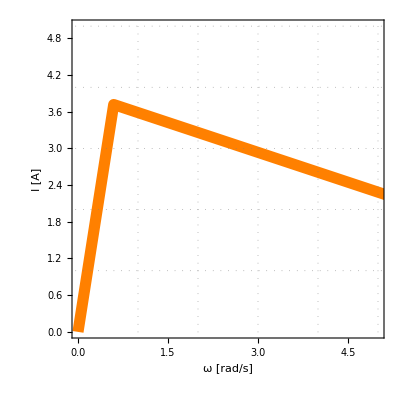

```mathematica
s=NDSolve[{x'[t]==f[t,x[t],y[t]][[1]],y'[t]==f[t,x[t],y[t]][[2]],x[0]==c1,y[0]==c2},{x,y},{t,Te},MaxStepSize->0.0001]
y[t]/.s/.t->Te
plotBIS=ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,20},PlotRange->{{0,5},{0,5}},FrameLabel->{"ω [rad/s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Monochrome",Frame->True,GridLines->{Table[i,{i,1,10}],Table[i,{i,1,10}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.02],Orange}]
```

#### Implicit Euler method (2^ndorder system)

```mathematica
Fx=AA-A-h f[tt,AA,BB][[1]];
Fy=BB-B-h f[tt,AA,BB][[2]];
F[tt_,AA_,BB_,t_,A_,B_]={Fx,Fy};
%//MatrixForm
```

(-A+AA-0.001 (-0.114962 AA+25.5904 BB)
-B-0.001 (103522.-8609.76 AA-26475.5 BB)+BB)

```mathematica
J[AA_,BB_]=Grad[F[tt,AA,BB,t,A,B],{AA,BB}];
%//MatrixForm
```

(1.00011 | -0.0255904
8.60976 | 27.4755)

{11.8573,0.0541438}

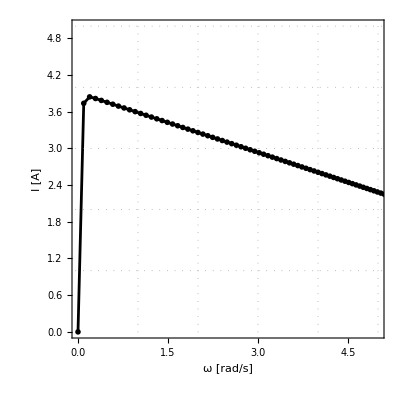

```mathematica
T=Table[t0+h i,{i,0,n}];  (*gridpoints: time*)Y=Table[0,{i,1,2},{j,1,n+1}];  (*gridpoints: x,y*)
Y[[All,1]]={c1,c2}; (*gridpoints: x,y*)
i=1;
For[i=1,i≤n,i++,                      (*external cycle: loading of Y[x,y]*)
Y[[All,i+1]]=Y[[All,i]];  (*0^th step: the previous value*)
For[j=1,j≤3,j++,                    (*internal cycle: Newton iteration*)
Y[[All,i+1]]=Y[[All,i+1]]-Inverse[J[Y[[1,i+1]],Y[[2,i+1]]]].F[T[[i+1]],Y[[1,i+1]],Y[[2,i+1]],T[[i]],Y[[1,i]],Y[[2,i]]]; (*x = x - J^-1(x).F(x)*)
]
]
Y//MatrixForm;
Y[[All,n+1]]
plotIE=ListPlot[Table[{Y[[1,i]],Y[[2,i]]},{i,1,n+1}],PlotRange->{{0,5},{0,5}},Mesh->Full, Joined->True,FrameLabel->{"ω [rad/s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Monochrome",Frame->True,GridLines->{Table[i,{i,1,10}],Table[i,{i,1,10}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.005],Black},PlotLegends->Automatic]
```

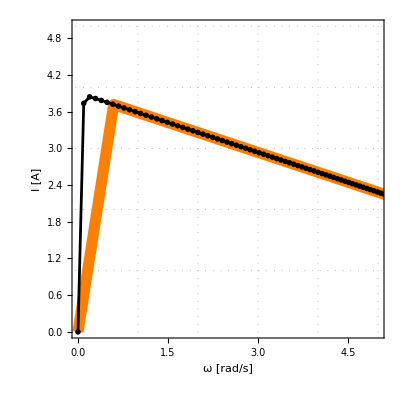

```mathematica
Show[plotBIS,plotIE]
```

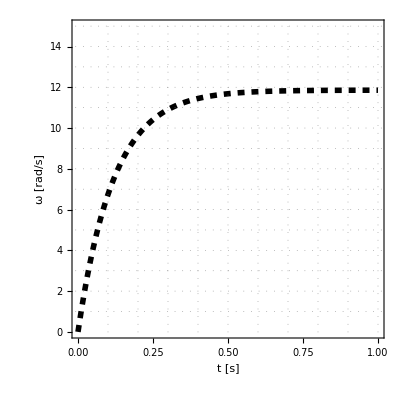

```mathematica
RotationalSpeedNumeric=ListLinePlot[Table[{T[[i]],Y[[1,i]]},{i,1,n+1,1}],PlotRange->{{0,1},{0,15}},FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.1,1,0.1}],Table[i,{i,1,15}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.01],Black,Dashed}]
```

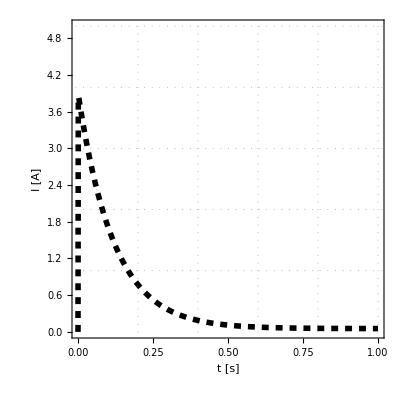

```mathematica
ArmatureCurrentNumeric=ListLinePlot[Table[{T[[i]],Y[[2,i]]},{i,1,n+1,1}],PlotRange->{{0,1},{0,5}},FrameLabel->{"t [s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.2,1,0.2}],Table[i,{i,1,10}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.01],Black,Dashed}]
```

Analytic Solution of the model equations

### Model parameters (estimated with MATLAB)

```mathematica
θ=0.038999801486034;
b=0.004483480554580;
K=0.998019215315511;
R=3.068968068446540;
L=0;
V=12;
TL= 0;
```

### Model equations (x→ω[rad/s], y→i[A])

```mathematica
MomentEquation = θ x'[t] +b x[t] == K y[t]-TL
KirchoffEquation = L y'[t]+R y[t] ==V-K x[t]
```

0.00448348 x[t]+0.0389998 x'[t]==0.998019 y[t]

3.06897 y[t]==12-0.998019 x[t]

```mathematica
CombinedEquation = MomentEquation/.Solve[KirchoffEquation,y[t]][[1]]//Simplify
```

1. x[t]+0.118527 x'[t]==11.86

```mathematica
solution = DSolve[{CombinedEquation,x[0]==0},x[t],t]
```

{{x[t]→11.86 ⅇ^(-8.43687 t) (-1.+1. ⅇ^(8.43687 t))}}

```mathematica
RotationalSpeedAnalytic = x[t]/.solution[[1]]//Simplify
```

11.86-11.86 ⅇ^(-8.43687 t)

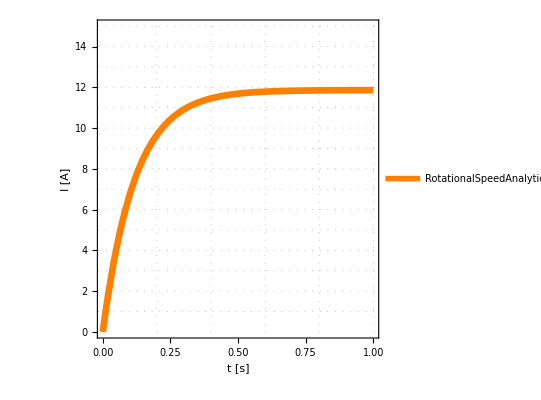

```mathematica
RotationalSpeedAnalyticPlot = Plot[RotationalSpeedAnalytic,{t,0,1},PlotRange->{{0,1},{0,15}},FrameLabel->{"t [s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.2,1,0.2}],Table[i,{i,1,15}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.012],Orange}]
```

```mathematica
ArmatureCurrentAnalytic = y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify
```

0.0532795+3.85683 ⅇ^(-8.43687 t)

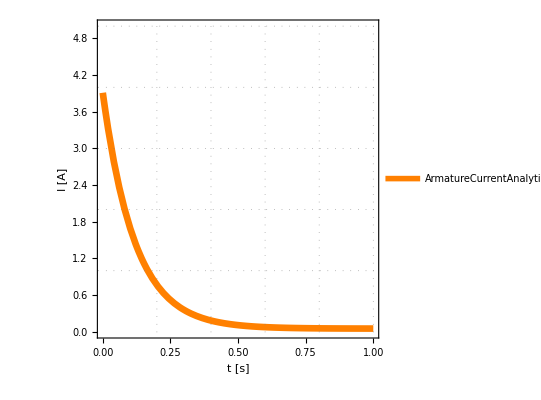

```mathematica
ArmatureCurrentAnalyticPlot = Plot[ArmatureCurrentAnalytic,{t,0,1},PlotRange->{{0,1},{0,5}},FrameLabel->{"t [s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.2,1,0.2}],Table[i,{i,1,15}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.012],Orange}]
```

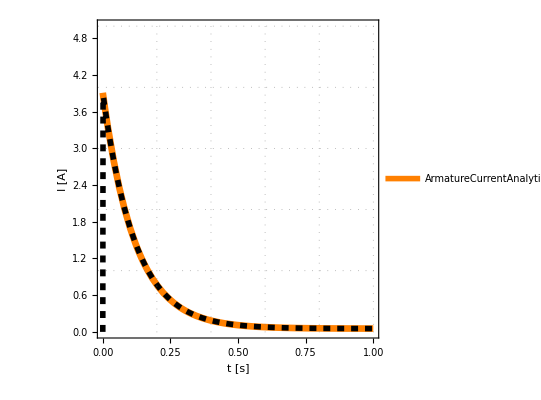

```mathematica
Show[ArmatureCurrentAnalyticPlot,ArmatureCurrentNumeric]
```

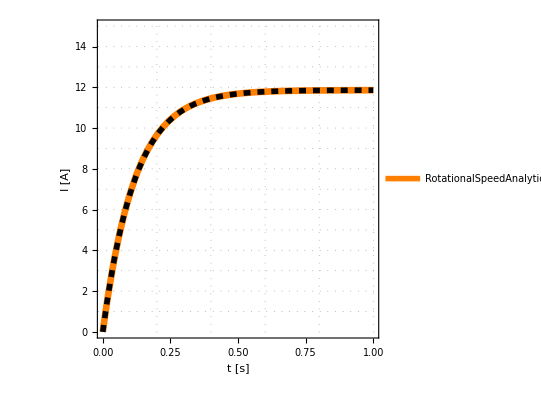

```mathematica
Show[RotationalSpeedAnalyticPlot,RotationalSpeedNumeric]
```

```mathematica
TorqueAnalytic = K y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify
```

0.053174+3.84919 ⅇ^(-8.43687 t)

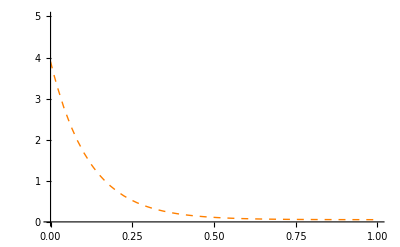

```mathematica
TorqueAnalyticPlot = Plot[TorqueAnalytic,{t,0,1},PlotRange->{0,5},PlotStyle->{Dashed,Orange,Thick}]
```